My growing list of utility functions I keep copy and pasting everywhere

```mathematica
xyrtoabbc[{x_,y_,r_}]:={r(x^2/r^2+y^2/r^2-1),1/r,x/r,y/r}
graphFromG[G_]:=PlanarGraph[AdjacencyGraph[If[#==-1,1,0]&/@#&/@G,VertexLabels->"Name"]]
abbctoxyr[{bt_,b_,h1_,h2_}]:={h1/b,h2/b,1/b}
graphDuals[circs_]:=Graphics[{Red,Dashed,Circle[{#⟦1⟧,#⟦2⟧},Abs[#⟦3⟧]]&/@circs}]
graphCircles[circs_]:=Graphics[Circle[{#⟦1⟧,#⟦2⟧},Abs[#⟦3⟧]]&/@circs]
graphAbbc[circs_]:=graphCircles[abbctoxyr/@circs]
graphDualAbbc[circs_]:=graphDuals[abbctoxyr/@circs]
findRoot[tuple_,sigmas_]:=Block[{candidates},
candidates=Select[sigmas,Total[#.tuple]<Total[tuple]&];
If[Length[candidates]==0,tuple,findRoot[candidates⟦1⟧.tuple,sigmas]]]
reflectx:={{1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, -1, 0}, {0, 0, 0, 1}}
reflecty:={{1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, 1, 0}, {0, 0, 0, -1}}
scale[a_]:={{a, 0, 0, 0}, {0, 1/a, 0, 0}, {0, 0, 1, 0}, {0, 0, 0, 1}}
rotate[θ_]:={{1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, Cos[θ], Sin[θ]}, {0, 0, -Sin[θ], Cos[θ]}}
translate[s_,t_]:={{1, s^2+t^2, 2s, 2t}, {0, 1, 0, 0}, {0, s, 1, 0}, {0, t, 0, 1}}
invert:={{0, 1, 0, 0}, {1, 0, 0, 0}, {0, 0, 1, 0}, {0, 0, 0, 1}}
invertAboutCircle[{x_,y_,r_}]:=translate[x,y].scale[r].{{0, 1, 0, 0}, {1, 0, 0, 0}, {0, 0, 1, 0}, {0, 0, 0, 1}}.scale[1/r].translate[-x,-y]
invertAboutAbbc[{bt_,b_,h1_,h2_}]:=invertAboutCircle[abbctoxyr[{bt,b,h1,h2}]]
```

Function to find root tuple just given G. It needs to know three rows of G corresponding to three circles on a face. It defaults to {1, 2, 3}, but you can change that with Face->whatever. Likewise, it will default to inverting through circle 4 to make the bounded packing, but you can change that with Invert->whatever. I’d recommend not picking anything on the face, since two of them don’t work as they are lines and the other can often give extra unwanted symmetry. Finally, it defaults to doing everything numerically, but you can make it exact by specifying Exact->True.

```mathematica
Options[rootTupleFromG]={"Face"->{1,2,3},"Invert"->4,"Exact"->False};
rootTupleFromG[G_,OptionsPattern[]]:=Block[{circs,P,v,c1,c2,c3,face,invert,exact},
P={{0, -1/2, 0, 0}, {-1/2, 0, 0, 0}, {0, 0, 1, 0}, {0, 0, 0, 1}};
face=OptionValue["Face"];
invert=OptionValue["Invert"];
exact=OptionValue["Exact"];
v={bt,b,h1,h2};
c1=face[[1]];
c2=face[[2]];
c3=face[[3]];
circs=Range[Length[G]];
circs[[c1]]={2,0,0,1};
circs[[c2]]={0,0,0,-1};
circs[[c3]]={(1-G[[c2,c3]]^2)/(G[[c1,c3]]+G[[c2,c3]]),-G[[c1,c3]]-G[[c2,c3]],0,-G[[c2,c3]]};
For[i=1,i<=Length[G],i++,
If[Not[MemberQ[i,face]],
circs[[i]]=v/.(If[exact,Solve,NSolve][circs[[c1]].P.v==G[[c1,i]]&&circs[[c2]].P.v==G[[c2,i]]&&circs[[c3]].P.v==G[[c3,i]]&&h1^2+h2^2-b bt==1,{bt,b,h1,h2}][[1]]);
]
];
invertAboutAbbc[circs[[invert]]].#&/@circs
]
```

```mathematica
icos={{1,-1,-4-Sqrt[5],-1,-2-Sqrt[5],-1,-2-Sqrt[5],-2-Sqrt[5],-1,-1,-2-Sqrt[5],-2-Sqrt[5]},{-1,1,-2-Sqrt[5],-2-Sqrt[5],-1,-1,-4-Sqrt[5],-2-Sqrt[5],-2-Sqrt[5],-1,-2-Sqrt[5],-1},{-4-Sqrt[5],-2-Sqrt[5],1,-2-Sqrt[5],-1,-2-Sqrt[5],-1,-1,-2-Sqrt[5],-2-Sqrt[5],-1,-1},{-1,-2-Sqrt[5],-2-Sqrt[5],1,-4-Sqrt[5],-2-Sqrt[5],-1,-1,-1,-1,-2-Sqrt[5],-2-Sqrt[5]},{-2-Sqrt[5],-1,-1,-4-Sqrt[5],1,-1,-2-Sqrt[5],-2-Sqrt[5],-2-Sqrt[5],-2-Sqrt[5],-1,-1},{-1,-1,-2-Sqrt[5],-2-Sqrt[5],-1,1,-2-Sqrt[5],-4-Sqrt[5],-1,-2-Sqrt[5],-1,-2-Sqrt[5]},{-2-Sqrt[5],-4-Sqrt[5],-1,-1,-2-Sqrt[5],-2-Sqrt[5],1,-1,-1,-2-Sqrt[5],-1,-2-Sqrt[5]},{-2-Sqrt[5],-2-Sqrt[5],-1,-1,-2-Sqrt[5],-4-Sqrt[5],-1,1,-2-Sqrt[5],-1,-2-Sqrt[5],-1},{-1,-2-Sqrt[5],-2-Sqrt[5],-1,-2-Sqrt[5],-1,-1,-2-Sqrt[5],1,-2-Sqrt[5],-1,-4-Sqrt[5]},{-1,-1,-2-Sqrt[5],-1,-2-Sqrt[5],-2-Sqrt[5],-2-Sqrt[5],-1,-2-Sqrt[5],1,-4-Sqrt[5],-1},{-2-Sqrt[5],-2-Sqrt[5],-1,-2-Sqrt[5],-1,-1,-1,-2-Sqrt[5],-1,-4-Sqrt[5],1,-2-Sqrt[5]},{-2-Sqrt[5],-1,-1,-2-Sqrt[5],-1,-2-Sqrt[5],-2-Sqrt[5],-1,-4-Sqrt[5],-1,-2-Sqrt[5],1}};
```

```mathematica
root=rootTupleFromG[icos,"Invert"->3,"Face"->{1,2,10},"Exact"->True]//FullSimplify
```

{{6 (9+4 √5),68+28 √5,-4 (13+6 √5),3 (9+4 √5)},{4 (9+4 √5),44+20 √5,-4 (9+4 √5),17+8 √5},{-2 (2+√5),-2 (3+√5),2 (2+√5),-2-√5},{39+17 √5,47+21 √5,-37-17 √5,20+9 √5},{11+5 √5,5 (3+√5),-11-5 √5,5+2 √5},{39+17 √5,46+20 √5,-37-17 √5,19+8 √5},{14+6 √5,6 (3+√5),-6 (2+√5),8+3 √5},{11+5 √5,16+6 √5,-11-5 √5,3 (2+√5)},{40+18 √5,47+21 √5,-39-17 √5,20+9 √5},{4 (9+4 √5),46+20 √5,-4 (9+4 √5),19+8 √5},{14+6 √5,16+6 √5,-6 (2+√5),3 (2+√5)},{10+4 √5,5 (3+√5),-9-5 √5,5+2 √5}}

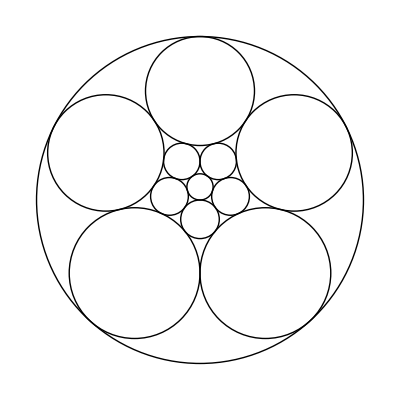

```mathematica
graphAbbc[root]
```